# Cases per Lawyer Data Collapse

We plot the number of lawyer of specific specialty as a function of a proxy of their number of cases across MSAs.

## Import Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\ol2234\Downloads\Lawyers\Figures\Affordability

## Affordability Spearman

```mathematica
SpearmanData=Import["Annual_Affordability_Spearman_All.csv"];
```

```mathematica
SpearmanData[[1]]
```

{Year,Profession,Spearman Rho,p_Value,Number of MSAs}

```mathematica
nThreshold=150;
```

```mathematica
filteredSpearmanData=Select[Rest[SpearmanData],Last[#]>nThreshold&];
```

```mathematica
Years=DeleteDuplicates[SpearmanData[[All,1]][[2;;]]]
```

{2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2021,2022,2023,2024}

```mathematica
Professions=DeleteDuplicates[filteredSpearmanData[[All,2]]]
```

{Child, family, and school social workers,Educational, vocational, and school counselors,Lawyers,Medical and public health social workers,Occupational therapists,Pharmacists,Physical therapists,Speech-language pathologists}

```mathematica
Spearman=KeyValueMap[{#1,#2[[All,{1,3}]]}&,GroupBy[filteredSpearmanData,#[[2]]&]][[All,2]];
```

```mathematica
pValue=KeyValueMap[{#1,#2[[All,{1,4}]]}&,GroupBy[filteredSpearmanData,#[[2]]&]][[All,2]];
```

## Average Affordability

```mathematica
AffordabilityData=Import["Annual_Average_Affordability_All.csv"];
```

```mathematica
AffordabilityData[[1]]
```

{year,OCC_TITLE,A_Afford_Weighted,H_Afford_Weighted}

```mathematica
filteredAffordabilityData=Select[Rest[AffordabilityData],MemberQ[Professions,#[[2]]]&];
```

```mathematica
Affordability=KeyValueMap[{#1,#2[[All,{1,3}]]}&,GroupBy[filteredAffordabilityData,#[[2]]&]][[All,2]];
```

## Plotting

## Parameters

```mathematica
TextSize=20;
```

```mathematica
TicksSize=15;
```

```mathematica
MarkerThickness=1/40;
```

```mathematica
LinesThickness=0.007;
```

```mathematica
PlotSize=500;
```

```mathematica
ColorsDiscrete=ResourceFunction["HexToColor"]/@{"#1065AB","#3893C3","#8EC4DE","#F6A482","#D75F4C","#B31529"}
```

{RGBColor[0.06274509803921569, 0.396078431372549, 0.6705882352941176],RGBColor[0.2196078431372549, 0.5764705882352941, 0.7647058823529411],RGBColor[0.5568627450980392, 0.7686274509803921, 0.8705882352941177],RGBColor[0.9647058823529412, 0.6431372549019607, 0.5098039215686274],RGBColor[0.8431372549019608, 0.37254901960784315, 0.2980392156862745],RGBColor[0.7019607843137254, 0.08235294117647059, 0.16078431372549018]}

```mathematica
ColorGradient=Blend[ColorsDiscrete,#]&
```

Blend[ColorsDiscrete,#1]&

```mathematica
colors=ColorGradient/@Rescale[Range[Length[Professions]]]
```

{RGBColor[0.06274509803921569, 0.396078431372549, 0.6705882352941176],RGBColor[0.17478991596638654, 0.5249299719887954, 0.7378151260504201],RGBColor[0.36414565826330536, 0.6588235294117647, 0.8100840336134454],RGBColor[0.6151260504201681, 0.7507002801120447, 0.819047619047619],RGBColor[0.9064425770308123, 0.661064425770308, 0.561344537815126],RGBColor[0.8952380952380953, 0.48851540616246497, 0.3887955182072829],RGBColor[0.8028011204481793, 0.2896358543417367, 0.2588235294117647],RGBColor[0.7019607843137254, 0.08235294117647059, 0.16078431372549018]}

```mathematica
colors=ResourceFunction["HexToColor"]/@{"#9AB4D9","#7BD119","#808080","#F5BFA9","#9587E6","#BEEBCC","#91E4F5","#E66576"}
```

{RGBColor[0.6039215686274509, 0.7058823529411764, 0.8509803921568627],RGBColor[0.4823529411764706, 0.8196078431372549, 0.09803921568627451],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.9607843137254902, 0.7490196078431373, 0.6627450980392157],RGBColor[0.5843137254901961, 0.5294117647058824, 0.9019607843137255],RGBColor[0.7450980392156863, 0.9215686274509803, 0.8],RGBColor[0.5686274509803921, 0.8941176470588235, 0.9607843137254902],RGBColor[0.9019607843137255, 0.396078431372549, 0.4627450980392157]}

```mathematica
colors=ResourceFunction["HexToColor"]/@{"#E6B0AA","#D1D1D1","#808080","#bae6ff","#9ef0f0","#d4bbff","#A3C4FF","#F9C0D9","#B2E7C0","#B697FF","#8EDAD9"}
```

{RGBColor[0.9019607843137255, 0.6901960784313725, 0.6666666666666666],RGBColor[0.8196078431372549, 0.8196078431372549, 0.8196078431372549],RGBColor[0.5019607843137255, 0.5019607843137255, 0.5019607843137255],RGBColor[0.7294117647058823, 0.9019607843137255, 1.],RGBColor[0.6196078431372549, 0.9411764705882353, 0.9411764705882353],RGBColor[0.8313725490196078, 0.7333333333333333, 1.],RGBColor[0.6392156862745098, 0.7686274509803921, 1.],RGBColor[0.9764705882352941, 0.7529411764705882, 0.8509803921568627],RGBColor[0.6980392156862745, 0.9058823529411765, 0.7529411764705882],RGBColor[0.7137254901960784, 0.592156862745098, 1.],RGBColor[0.5568627450980392, 0.8549019607843137, 0.8509803921568627]}

```mathematica
opacity=1;
```

```mathematica
myLegend=PointLegend[colors,Professions,LegendMarkers->Table[{Graphics[{FaceForm[colors[[i]]],EdgeForm[{colors[[i]],Opacity[opacity]}],If[i==3,Polygon[{{0,0.8},{-0.7,-0.4},{0.7,-0.4}}],Disk[{0,0},0.6]]},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],15},{i,Length[colors]}],LegendMarkerSize->{20,20},LabelStyle->Directive[FontFamily->"Arial",FontSize->TicksSize],LegendLayout->{"Column",2}]
```

## Plotting

## Affordability Spearman

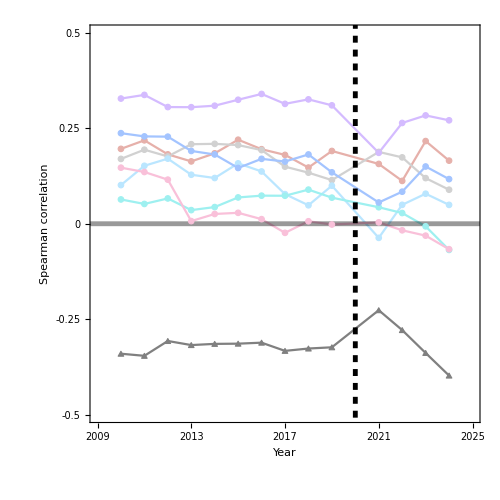

```mathematica
SpearmanPlot=ListPlot[Spearman,PlotRange->{{Min[Years]-1,Max[Years]+1},{-0.5,0.5}},Joined->True,PlotStyle->colors,PlotMarkers->Table[{Graphics[{FaceForm[colors[[i]]],EdgeForm[{colors[[i]],Opacity[opacity]}],If[i==3,Polygon[{{0,1.0},{-0.9,-0.6},{0.9,-0.6}}],Disk[{0,0},0.8]]},PlotRange->{{-1.2,1.2},{-1.2,1.2}}],MarkerThickness},{i,1,Length[colors]}],PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{-1,-0.5,-0.25,0,0.25,0.5,1},None},{Table[2009+4*i,{i,0,4}],None}},FrameLabel->{Style["Year",TextSize],Style["Spearman correlation",TextSize]},GridLines->{None,{0}},GridLinesStyle->Directive[Black,Thickness[LinesThickness],Opacity[0.4]],PlotTheme-> "Scientific", 
FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Courier"}],AspectRatio->1,ImageSize->PlotSize,Epilog->{{Black,Dashed,Thickness[LinesThickness],Line[{{2020,-1},{2020,1}}]}}]
```

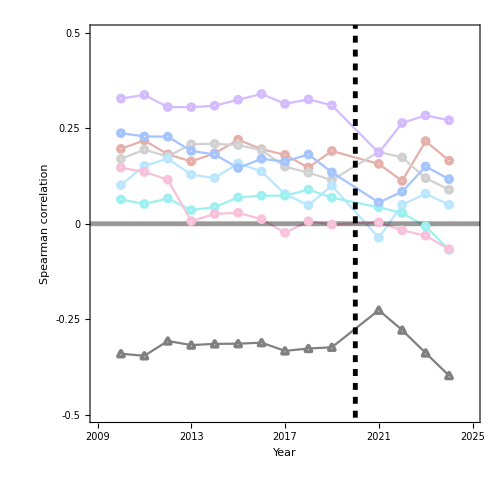

```mathematica
SpearmanPlotHollow=ListPlot[Spearman,PlotRange->{{Min[Years]-1,Max[Years]+1},{-0.5,0.5}},Joined->True,PlotStyle->colors,PlotMarkers->Table[{Graphics[{FaceForm[White],EdgeForm[{colors[[i]],Opacity[1],Thickness[0.15]}],If[i==3,Polygon[{{0,1.3},{-1.1,-0.8},{1.1,-0.8}}],Disk[{0,0},0.9]]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],MarkerThickness},{i,1,Length[colors]}],PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{-1,-0.5,-0.25,0,0.25,0.5,1},None},{Table[2009+4*i,{i,0,4}],None}},FrameLabel->{Style["Year",TextSize],Style["Spearman correlation",TextSize]},GridLines->{None,{0}},GridLinesStyle->Directive[Black,Thickness[LinesThickness],Opacity[0.4]],PlotTheme->"Scientific",FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Courier"}],AspectRatio->1,ImageSize->PlotSize,Epilog->{{Black,Dashed,Thickness[LinesThickness],Line[{{2020,-1},{2020,1}}]}}]
```

```mathematica
alpha=0.05;
```

```mathematica
significantSpearman=Table[Table[If[pValue[[i,j,2]]<=alpha,Spearman[[i,j]],Null],{j,1,Length[Spearman[[i]]]}],{i,1,Length[Spearman]}];
```

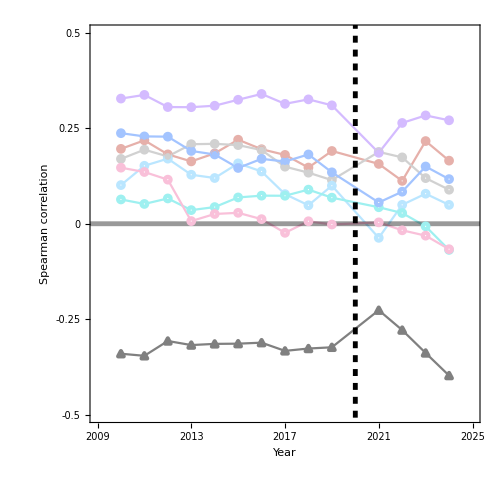

```mathematica
SpearmanPlot=Show[SpearmanPlotHollow,ListPlot[significantSpearman,PlotStyle->colors,PlotMarkers->Table[{Graphics[{FaceForm[colors[[i]]],EdgeForm[{colors[[i]],Opacity[opacity]}],If[i==3,Polygon[{{0,1.3},{-1.1,-0.8},{1.1,-0.8}}],Disk[{0,0},0.9]]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],MarkerThickness},{i,1,Length[colors]}]]]
```

## Average Affordability

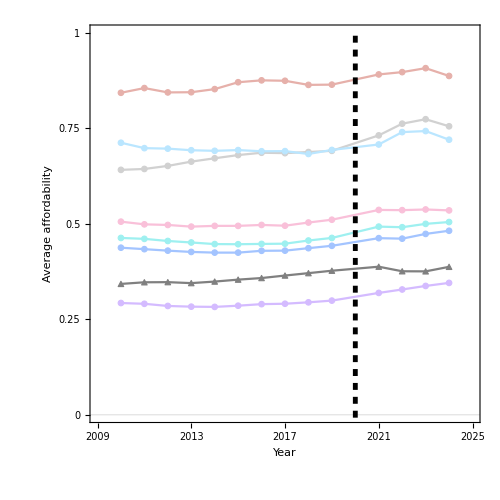

```mathematica
SpearmanPlot=ListPlot[Affordability,PlotRange->{{Min[Years]-1,Max[Years]+1},{0,1}},Joined->True,PlotStyle->colors,PlotMarkers->Table[{Graphics[{FaceForm[colors[[i]]],EdgeForm[{colors[[i]],Opacity[opacity]}],If[i==3,Polygon[{{0,1.3},{-1.1,-0.8},{1.1,-0.8}}],Disk[{0,0},0.9]]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],MarkerThickness},{i,1,Length[colors]}],PlotTheme->"Scientific",FrameTicksStyle->Directive["Label",TextSize],FrameTicks->{{{0,0.25,0.5,0.75,1},None},{Table[2009+4*i,{i,0,4}],None}},FrameLabel->{Style["Year",TextSize],Style["Average affordability",TextSize]},PlotTheme->"Scientific",FrameStyle->Directive[Thickness[.005]],LabelStyle->Directive[Black,FontFamily->{"Courier"}],AspectRatio->1,ImageSize->PlotSize,Epilog->{{Black,Dashed,Thickness[LinesThickness],Line[{{2020,-1},{2020,1}}]}}]
```